## Analytical Solution

Tana = 1/4 (1+x+4 Cos[(π x)/2])

qana = 1/4 (-1+2 π Sin[(π x)/2])

xTmax = (2 ArcSin[1/(2 π)])/π

xqmax = 1

Tmax = 1/4 (1+4 √(1-1/(4 π^2))+(2 ArcSin[1/(2 π)])/π)

qmax = 1/4 (-1+2 π)

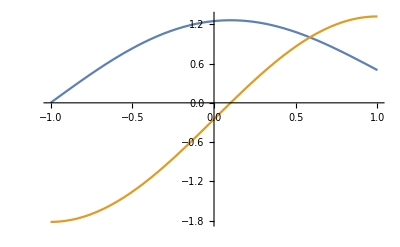

```mathematica
Q[x_]=π^2/4 Cos[(π x)/2];
κ=1;
sol=DSolve[{T''[x]==-Q[x]/κ,T[-1]==0,T[1]==1/2},T[x],x][[1]];
t[x_]=T[x]/.sol;
q[x_]=-κ t'[x];

xTmax=Union[Abs[Re[Select[(x/.Solve[t'[x]==0,x])/.{C[1]->0},-1≤Re[#]&&Re[#]≤1&]]]][[1]]//Simplify;
xqmax=Union[Abs[Re[Select[(x/.Solve[q'[x]==0,x])/.{C[1]->0},-1≤Re[#]&&Re[#]≤1&]]]][[1]];

Print["Tana = ",t[x]]
Print["qana = ",q[x]]
Print["xTmax = ",xTmax]
Print["xqmax = ",xqmax]
Print["Tmax = ",t[xTmax]]
Print["qmax = ",q[xqmax]]

Plot[{t[x],-t'[x]},{x,-1,1}]
```

## Finite Elements

### Linear Elements: Temperature-Heat Flux System

```mathematica
w[x_]={(xi-x)/(xi-xim1),(x-xim1)/(xi-xim1)};
s[x_]=w[x];
stiff1[x_]=Outer[Times,w[x],Join[D[w[x],{x,1}],{0,0}]];
stiff2[x_]=Outer[Times,w[x],Join[w[x],k D[w[x],{x,1}]]];
stiff[x_]=Join[stiff1[x],stiff2[x]];

ui={qim1,qi,Tim1,Ti};
shift={1,3,2,4};
ui=ui[[shift]];
stiff[x_]=stiff[x][[{3,1,4,2},shift]];
kij=∫_xim1^xi stiff[x]ⅆx/.{xi-> xim1+Δxi};

bi=Join[∫_xim1^xi w[x]Q[x]ⅆx/.{xi-xim1-> Δxi},{0,0}];
bi=bi[[{3,1,4,2}]];

kij//FullSimplify//MatrixForm
bi//FullSimplify//MatrixForm
ui//MatrixForm
```

(Δxi/3 | -k/2 | Δxi/6 | k/2
-1/2 | 0 | 1/2 | 0
Δxi/6 | -k/2 | Δxi/3 | k/2
-1/2 | 0 | 1/2 | 0)

(0
(-Cos[(π xi)/2]+Cos[(π xim1)/2])/Δxi-1/2 π Sin[(π xim1)/2]
0
(Cos[(π xi)/2]-Cos[(π xim1)/2])/Δxi+1/2 π Sin[(π xi)/2])

(qim1
Tim1
qi
Ti)

### Linear Elements : Temperature Only

```mathematica
w[x_]={(xi-x)/(xi-xim1),(x-xim1)/(xi-xim1)};
s[x_]=w[x];
stiff[x_]=Outer[Times,D[w[x],{x,1}],D[s[x],{x,1}]];

ui={Tim1,Ti};
shift={1,2};
ui=ui[[shift]];
stiff[x_]=stiff[x][[All,shift]];
kij=∫_xim1^xi stiff[x]ⅆx/.{xi-> xim1+Δxi};
bi=-∫_xim1^xi w[x]Q[x]ⅆx//FullSimplify;
ll=-(∫_xim1^xi w[x][[2]]Q[x]ⅆx+∫_xi^xip1 (w[x][[1]]/.{xim1->xi,xi->xip1})Q[x]ⅆx)/.{xim1-> xi-Δxi,xip1-> xi+Δxi}//FullSimplify
N[ll/.{Δxi->1/3,xi->-1/3},16]


kij//MatrixForm
bi//MatrixForm//FullSimplify
```

-(4 Cos[(π xi)/2] Sin[(π Δxi)/4]^2)/Δxi

-0.6961524227066319

(1/Δxi | -1/Δxi
-1/Δxi | 1/Δxi)

((Cos[(π xi)/2]-Cos[(π xim1)/2])/(xi-xim1)+1/2 π Sin[(π xim1)/2]
(-Cos[(π xi)/2]+Cos[(π xim1)/2])/(xi-xim1)-1/2 π Sin[(π xi)/2])

## Finite Differences

### Lagrange Interpolation

```mathematica
xs={xim1,xi,xip1};
ϕs={ϕim1,ϕi,ϕip1};
rules={xim2->xi-2Δxi,xim1->xi-Δxi,xip1->xi+Δxi,xip2->xi+2Δxi};
ϕ[x_]=(∑_(i=1)^Length[xs] ϕs[[i]]∏_(j=1)^Length[xs] If[i≠j,(x-xs[[j]])/(xs[[i]]-xs[[j]]),1])/.rules;
```

```mathematica
Print["ϕ[x] = ",ϕ[xi]//FullSimplify]
Print["ϕ'[x] = ",ϕ'[xi]//Expand]
Print["ϕ''[x] = ",ϕ''[xi]//Expand]
```

ϕ[x] = ϕi

ϕ'[x] = -ϕim1/(2 Δxi)+ϕip1/(2 Δxi)

ϕ''[x] = -(2 ϕi)/Δxi^2+ϕim1/Δxi^2+ϕip1/Δxi^2